## We shall use Mathematica to

#### Evaluate physics problems functions vector field physics problems; shm, n-hm,damped curve fitting calculus tools to solve differential equations monte carlo problem All exams on computer 30% midsem 50% endsem 20% quizzes

```mathematica
1+1

shift+enter for output
Plot[Sinx,{x,-10,-10}]
```

2

enter for output+shift

Plot::plld: Endpoints for x in {x,-10,-10} must have distinct machine-precision numerical values.

```mathematica
Plot[Sinx,{x,-10,-10}]
```

Plot::plld: Endpoints for x in {x,-10,-10} must have distinct machine-precision numerical values.

Plot[Sinx,{x,-10,-10}]

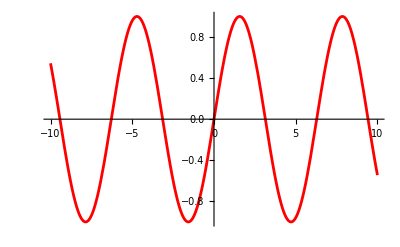

Plot::nonopt: Options expected (instead of {x,-10,10}) beyond position 2 in Plot[Sin[x],Cos[x],{x,-10,10}]. An option must be a rule or a list of rules.

```mathematica
Plot[Sin[x],{x,-10,10},PlotStyle->Red]
```

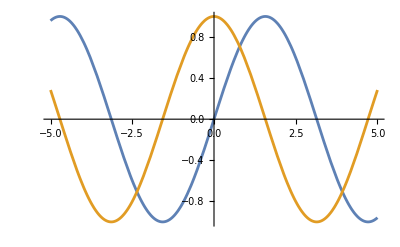

```mathematica
Plot[ {Sin[u], Cos[u]},{u,-5,5}]
```

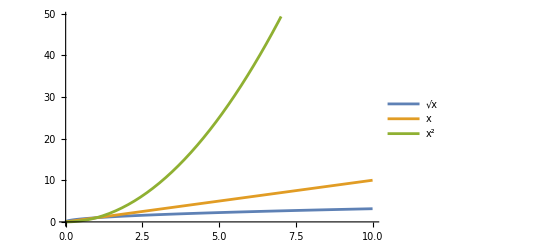

```mathematica
Plot[{x^(1/2),x,x^2},{x,0,10},PlotLegends->"Expressions"]
```

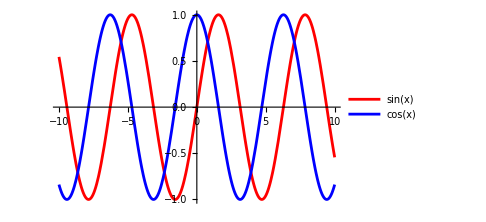

```mathematica
Plot[{Sin[x],Cos[x]},{x,-10,10},PlotStyle->{Red,Blue},PlotLegends->"Expressions",ImageSize->Medium,Axes->True,Filling->"Axis"]
```

```mathematica
Table[1,10]
```

{1,1,1,1,1,1,1,1,1,1}

```mathematica
{1, 1, 1, 1, 1, 1, 1, 1, 1, 1}
```

{1,1,1,1,1,1,1,1,1,1}

```mathematica
Table[n!,{n,1,20}]
```

{1,2,6,24,120,720,5040,40320,362880,3628800,39916800,479001600,6227020800,87178291200,1307674368000,20922789888000,355687428096000,6402373705728000,121645100408832000,2432902008176640000}

```mathematica
Table[n,{n,1,10}]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
x=20!
```

2432902008176640000

```mathematica
v=Table[n!,{n,1,3}]
```

{1,2,6}

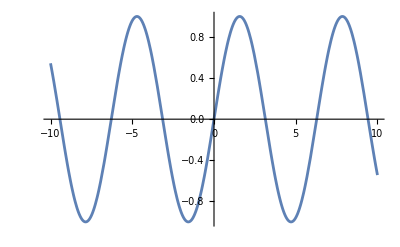
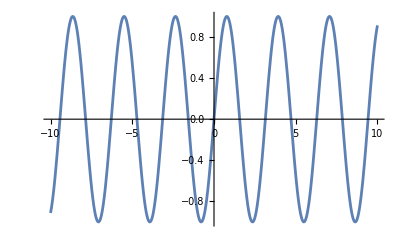
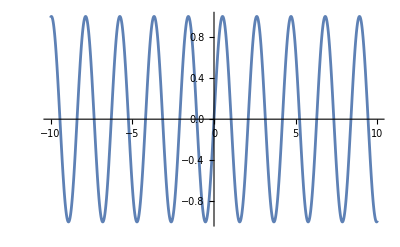
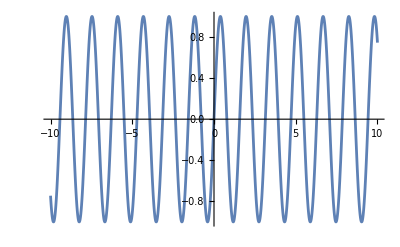

```mathematica
Table[Plot[Sin[n*y],{y,-10,10}],{n,1,4}]
```

```mathematica
factorial=Table[n!,{n,1,10}]
```

{1,2,6,24,120,720,5040,40320,362880,3628800}

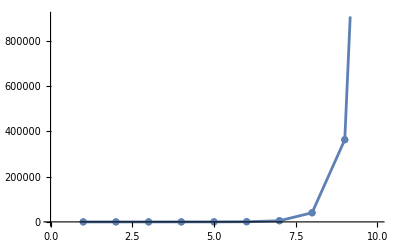

```mathematica
ListPlot[factorial,Joined->True,Mesh->Full]
```

```mathematica
n!,4^n,n^x
```

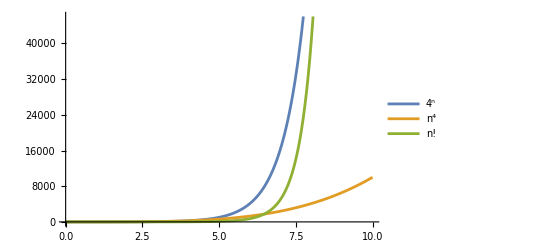

```mathematica
Plot[{4^n,n^4,n!},{n,0,10},PlotLegends->"Expressions"]
```

```mathematica
polynomial=Table[n^4,{n,1,10}]
```

{1,16,81,256,625,1296,2401,4096,6561,10000}

```mathematica
exponentials=Table[4^n,{n,1,10}]
```

{4,16,64,256,1024,4096,16384,65536,262144,1048576}

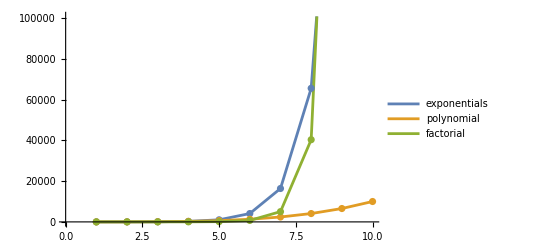

```mathematica
ListPlot[{exponentials,polynomial,factorial},Joined->True,Mesh->All,PlotLegends->{"exponentials","polynomial","factorial"}]
```

```mathematica
(*manupilate helps to play with the variables. Gyan rizz!!!*)
```

```mathematica
Manipulate[n,{n,1,10}]
```

```mathematica
Manipulate[Plot[Sin[n*x],{x,-10,10}],{n,0,1}]
```

```mathematica
(*Roots of a function*)
```

```mathematica
Plot[4*x^3-12*x^2+1,{x,-2,5}]
```

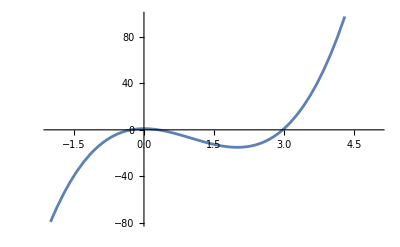

```mathematica
(*To find the exact root;*)
```

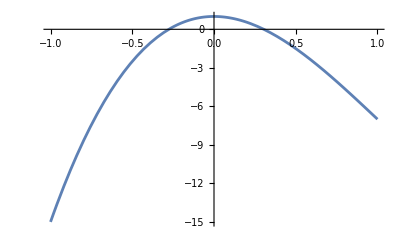

```mathematica
Plot[4*x^3-12*x^2+1,{x,-1,1}]
```

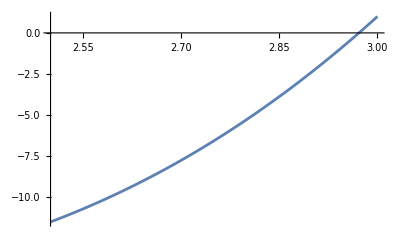

```mathematica
Plot[4*x^3-12*x^2+1,{x,2.5,3}]
```

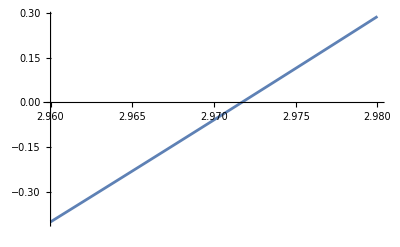

```mathematica
Plot[4*x^3-12*x^2+1,{x,2.96,2.98}]
```

```mathematica
Table[{x,x^3-4x^2+1},{x,0.5,0.6,0.001}]
```

{{0.5,0.125},{0.501,0.121748},{0.502,0.11849},{0.503,0.115228},{0.504,0.11196},{0.505,0.108688},{0.506,0.10541},{0.507,0.102128},{0.508,0.0988405},{0.509,0.0955482},{0.51,0.092251},{0.511,0.0889488},{0.512,0.0856417},{0.513,0.0823297},{0.514,0.0790127},{0.515,0.0756909},{0.516,0.0723641},{0.517,0.0690324},{0.518,0.0656958},{0.519,0.0623544},{0.52,0.059008},{0.521,0.0556568},{0.522,0.0523006},{0.523,0.0489397},{0.524,0.0455738},{0.525,0.0422031},{0.526,0.0388276},{0.527,0.0354472},{0.528,0.032062},{0.529,0.0286719},{0.53,0.025277},{0.531,0.0218773},{0.532,0.0184728},{0.533,0.0150634},{0.534,0.0116493},{0.535,0.00823038},{0.536,0.00480666},{0.537,0.00137815},{0.538,-0.00205513},{0.539,-0.00549318},{0.54,-0.008936},{0.541,-0.0123836},{0.542,-0.0158359},{0.543,-0.019293},{0.544,-0.0227548},{0.545,-0.0262214},{0.546,-0.0296927},{0.547,-0.0331687},{0.548,-0.0366494},{0.549,-0.0401349},{0.55,-0.043625},{0.551,-0.0471198},{0.552,-0.0506194},{0.553,-0.0541236},{0.554,-0.0576325},{0.555,-0.0611461},{0.556,-0.0646644},{0.557,-0.0681873},{0.558,-0.0717149},{0.559,-0.0752471},{0.56,-0.078784},{0.561,-0.0823255},{0.562,-0.0858717},{0.563,-0.0894225},{0.564,-0.0929779},{0.565,-0.0965379},{0.566,-0.100103},{0.567,-0.103672},{0.568,-0.107246},{0.569,-0.110824},{0.57,-0.114407},{0.571,-0.117995},{0.572,-0.121587},{0.573,-0.125183},{0.574,-0.128785},{0.575,-0.132391},{0.576,-0.136001},{0.577,-0.139616},{0.578,-0.143235},{0.579,-0.146859},{0.58,-0.150488},{0.581,-0.154121},{0.582,-0.157759},{0.583,-0.161401},{0.584,-0.165047},{0.585,-0.168698},{0.586,-0.172354},{0.587,-0.176014},{0.588,-0.179679},{0.589,-0.183348},{0.59,-0.187021},{0.591,-0.190699},{0.592,-0.194381},{0.593,-0.198068},{0.594,-0.201759},{0.595,-0.205455},{0.596,-0.209155},{0.597,-0.21286},{0.598,-0.216569},{0.599,-0.220282},{0.6,-0.224}}

```mathematica
Table[{x,x^3-4x^2+1},{x,0.537,0.538,0.00001}]
```

{{0.537,0.00137815},{0.53701,0.00134384},{0.53702,0.00130953},{0.53703,0.00127522},{0.53704,0.00124091},{0.53705,0.0012066},{0.53706,0.00117229},{0.53707,0.00113798},{0.53708,0.00110367},{0.53709,0.00106935},{0.5371,0.00103504},{0.53711,0.00100073},{0.53712,0.000966411},{0.53713,0.000932097},{0.53714,0.000897781},{0.53715,0.000863465},{0.53716,0.000829149},{0.53717,0.000794832},{0.53718,0.000760515},{0.53719,0.000726197},{0.5372,0.000691879},{0.53721,0.00065756},{0.53722,0.000623241},{0.53723,0.000588921},{0.53724,0.000554601},{0.53725,0.00052028},{0.53726,0.000485959},{0.53727,0.000451638},{0.53728,0.000417316},{0.53729,0.000382993},{0.5373,0.00034867},{0.53731,0.000314347},{0.53732,0.000280023},{0.53733,0.000245698},{0.53734,0.000211373},{0.53735,0.000177048},{0.53736,0.000142722},{0.53737,0.000108396},{0.53738,0.0000740687},{0.53739,0.0000397414},{0.5374,5.41362×10^-6},{0.53741,-0.0000289147},{0.53742,-0.0000632434},{0.53743,-0.0000975726},{0.53744,-0.000131902},{0.53745,-0.000166233},{0.53746,-0.000200563},{0.53747,-0.000234894},{0.53748,-0.000269226},{0.53749,-0.000303558},{0.5375,-0.000337891},{0.53751,-0.000372224},{0.53752,-0.000406557},{0.53753,-0.000440891},{0.53754,-0.000475226},{0.53755,-0.000509561},{0.53756,-0.000543896},{0.53757,-0.000578232},{0.53758,-0.000612568},{0.53759,-0.000646905},{0.5376,-0.000681243},{0.53761,-0.00071558},{0.53762,-0.000749919},{0.53763,-0.000784258},{0.53764,-0.000818597},{0.53765,-0.000852937},{0.53766,-0.000887277},{0.53767,-0.000921617},{0.53768,-0.000955959},{0.53769,-0.0009903},{0.5377,-0.00102464},{0.53771,-0.00105898},{0.53772,-0.00109333},{0.53773,-0.00112767},{0.53774,-0.00116202},{0.53775,-0.00119636},{0.53776,-0.00123071},{0.53777,-0.00126505},{0.53778,-0.0012994},{0.53779,-0.00133374},{0.5378,-0.00136809},{0.53781,-0.00140244},{0.53782,-0.00143679},{0.53783,-0.00147113},{0.53784,-0.00150548},{0.53785,-0.00153983},{0.53786,-0.00157418},{0.53787,-0.00160853},{0.53788,-0.00164288},{0.53789,-0.00167723},{0.5379,-0.00171159},{0.53791,-0.00174594},{0.53792,-0.00178029},{0.53793,-0.00181464},{0.53794,-0.001849},{0.53795,-0.00188335},{0.53796,-0.00191771},{0.53797,-0.00195206},{0.53798,-0.00198642},{0.53799,-0.00202077},{0.538,-0.00205513}}

```mathematica
Table[{x,x^3-4x^2+1},{x,0.5374020,0.5374028,0.000000001}]
```

{{0.537402,-1.45199×10^-6},{0.537402,-1.45543×10^-6},{0.537402,-1.45886×10^-6},{0.537402,-1.46229×10^-6},{0.537402,-1.46572×10^-6},{0.537402,-1.46916×10^-6},{0.537402,-1.47259×10^-6},{0.537402,-1.47602×10^-6},{0.537402,-1.47946×10^-6},{0.537402,-1.48289×10^-6},{0.537402,-1.48632×10^-6},{0.537402,-1.48975×10^-6},{0.537402,-1.49319×10^-6},{0.537402,-1.49662×10^-6},{0.537402,-1.50005×10^-6},{0.537402,-1.50349×10^-6},{0.537402,-1.50692×10^-6},{0.537402,-1.51035×10^-6},{0.537402,-1.51378×10^-6},{0.537402,-1.51722×10^-6},{0.537402,-1.52065×10^-6},{0.537402,-1.52408×10^-6},{0.537402,-1.52751×10^-6},{0.537402,-1.53095×10^-6},{0.537402,-1.53438×10^-6},{0.537402,-1.53781×10^-6},{0.537402,-1.54125×10^-6},{0.537402,-1.54468×10^-6},{0.537402,-1.54811×10^-6},{0.537402,-1.55154×10^-6},{0.537402,-1.55498×10^-6},{0.537402,-1.55841×10^-6},{0.537402,-1.56184×10^-6},{0.537402,-1.56528×10^-6},{0.537402,-1.56871×10^-6},{0.537402,-1.57214×10^-6},{0.537402,-1.57557×10^-6},{0.537402,-1.57901×10^-6},{0.537402,-1.58244×10^-6},{0.537402,-1.58587×10^-6},{0.537402,-1.58931×10^-6},{0.537402,-1.59274×10^-6},{0.537402,-1.59617×10^-6},{0.537402,-1.5996×10^-6},{0.537402,-1.60304×10^-6},{0.537402,-1.60647×10^-6},{0.537402,-1.6099×10^-6},{0.537402,-1.61334×10^-6},{0.537402,-1.61677×10^-6},{0.537402,-1.6202×10^-6},{0.537402,-1.62363×10^-6},{0.537402,-1.62707×10^-6},{0.537402,-1.6305×10^-6},{0.537402,-1.63393×10^-6},{0.537402,-1.63736×10^-6},{0.537402,-1.6408×10^-6},{0.537402,-1.64423×10^-6},{0.537402,-1.64766×10^-6},{0.537402,-1.6511×10^-6},{0.537402,-1.65453×10^-6},{0.537402,-1.65796×10^-6},{0.537402,-1.66139×10^-6},{0.537402,-1.66483×10^-6},{0.537402,-1.66826×10^-6},{0.537402,-1.67169×10^-6},{0.537402,-1.67513×10^-6},{0.537402,-1.67856×10^-6},{0.537402,-1.68199×10^-6},{0.537402,-1.68542×10^-6},{0.537402,-1.68886×10^-6},{0.537402,-1.69229×10^-6},{0.537402,-1.69572×10^-6},{0.537402,-1.69916×10^-6},{0.537402,-1.70259×10^-6},{0.537402,-1.70602×10^-6},{0.537402,-1.70945×10^-6},{0.537402,-1.71289×10^-6},{0.537402,-1.71632×10^-6},{0.537402,-1.71975×10^-6},{0.537402,-1.72319×10^-6},{0.537402,-1.72662×10^-6},{0.537402,-1.73005×10^-6},{0.537402,-1.73348×10^-6},{0.537402,-1.73692×10^-6},{0.537402,-1.74035×10^-6},{0.537402,-1.74378×10^-6},{0.537402,-1.74721×10^-6},{0.537402,-1.75065×10^-6},{0.537402,-1.75408×10^-6},{0.537402,-1.75751×10^-6},{0.537402,-1.76095×10^-6},{0.537402,-1.76438×10^-6},{0.537402,-1.76781×10^-6},{0.537402,-1.77124×10^-6},{0.537402,-1.77468×10^-6},{0.537402,-1.77811×10^-6},{0.537402,-1.78154×10^-6},{0.537402,-1.78498×10^-6},{0.537402,-1.78841×10^-6},{0.537402,-1.79184×10^-6},{0.537402,-1.79527×10^-6},{0.537402,-1.79871×10^-6},{0.537402,-1.80214×10^-6},{0.537402,-1.80557×10^-6},{0.537402,-1.80901×10^-6},{0.537402,-1.81244×10^-6},{0.537402,-1.81587×10^-6},{0.537402,-1.8193×10^-6},{0.537402,-1.82274×10^-6},{0.537402,-1.82617×10^-6},{0.537402,-1.8296×10^-6},{0.537402,-1.83304×10^-6},{0.537402,-1.83647×10^-6},{0.537402,-1.8399×10^-6},{0.537402,-1.84333×10^-6},{0.537402,-1.84677×10^-6},{0.537402,-1.8502×10^-6},{0.537402,-1.85363×10^-6},{0.537402,-1.85706×10^-6},{0.537402,-1.8605×10^-6},{0.537402,-1.86393×10^-6},{0.537402,-1.86736×10^-6},{0.537402,-1.8708×10^-6},{0.537402,-1.87423×10^-6},{0.537402,-1.87766×10^-6},{0.537402,-1.88109×10^-6},{0.537402,-1.88453×10^-6},{0.537402,-1.88796×10^-6},{0.537402,-1.89139×10^-6},{0.537402,-1.89483×10^-6},{0.537402,-1.89826×10^-6},{0.537402,-1.90169×10^-6},{0.537402,-1.90512×10^-6},{0.537402,-1.90856×10^-6},{0.537402,-1.91199×10^-6},{0.537402,-1.91542×10^-6},{0.537402,-1.91886×10^-6},{0.537402,-1.92229×10^-6},{0.537402,-1.92572×10^-6},{0.537402,-1.92915×10^-6},{0.537402,-1.93259×10^-6},{0.537402,-1.93602×10^-6},{0.537402,-1.93945×10^-6},{0.537402,-1.94289×10^-6},{0.537402,-1.94632×10^-6},{0.537402,-1.94975×10^-6},{0.537402,-1.95318×10^-6},{0.537402,-1.95662×10^-6},{0.537402,-1.96005×10^-6},{0.537402,-1.96348×10^-6},{0.537402,-1.96692×10^-6},{0.537402,-1.97035×10^-6},{0.537402,-1.97378×10^-6},{0.537402,-1.97721×10^-6},{0.537402,-1.98065×10^-6},{0.537402,-1.98408×10^-6},{0.537402,-1.98751×10^-6},{0.537402,-1.99094×10^-6},{0.537402,-1.99438×10^-6},{0.537402,-1.99781×10^-6},{0.537402,-2.00124×10^-6},{0.537402,-2.00468×10^-6},{0.537402,-2.00811×10^-6},{0.537402,-2.01154×10^-6},{0.537402,-2.01497×10^-6},{0.537402,-2.01841×10^-6},{0.537402,-2.02184×10^-6},{0.537402,-2.02527×10^-6},{0.537402,-2.02871×10^-6},{0.537402,-2.03214×10^-6},{0.537402,-2.03557×10^-6},{0.537402,-2.039×10^-6},{0.537402,-2.04244×10^-6},{0.537402,-2.04587×10^-6},{0.537402,-2.0493×10^-6},{0.537402,-2.05274×10^-6},{0.537402,-2.05617×10^-6},{0.537402,-2.0596×10^-6},{0.537402,-2.06303×10^-6},{0.537402,-2.06647×10^-6},{0.537402,-2.0699×10^-6},{0.537402,-2.07333×10^-6},{0.537402,-2.07677×10^-6},{0.537402,-2.0802×10^-6},{0.537402,-2.08363×10^-6},{0.537402,-2.08706×10^-6},{0.537402,-2.0905×10^-6},{0.537402,-2.09393×10^-6},{0.537402,-2.09736×10^-6},{0.537402,-2.10079×10^-6},{0.537402,-2.10423×10^-6},{0.537402,-2.10766×10^-6},{0.537402,-2.11109×10^-6},{0.537402,-2.11453×10^-6},{0.537402,-2.11796×10^-6},{0.537402,-2.12139×10^-6},{0.537402,-2.12482×10^-6},{0.537402,-2.12826×10^-6},{0.537402,-2.13169×10^-6},{0.537402,-2.13512×10^-6},{0.537402,-2.13856×10^-6},{0.537402,-2.14199×10^-6},{0.537402,-2.14542×10^-6},{0.537402,-2.14885×10^-6},{0.537402,-2.15229×10^-6},{0.537402,-2.15572×10^-6},{0.537402,-2.15915×10^-6},{0.537402,-2.16259×10^-6},{0.537402,-2.16602×10^-6},{0.537402,-2.16945×10^-6},{0.537402,-2.17288×10^-6},{0.537402,-2.17632×10^-6},{0.537402,-2.17975×10^-6},{0.537402,-2.18318×10^-6},{0.537402,-2.18662×10^-6},{0.537402,-2.19005×10^-6},{0.537402,-2.19348×10^-6},{0.537402,-2.19691×10^-6},{0.537402,-2.20035×10^-6},{0.537402,-2.20378×10^-6},{0.537402,-2.20721×10^-6},{0.537402,-2.21064×10^-6},{0.537402,-2.21408×10^-6},{0.537402,-2.21751×10^-6},{0.537402,-2.22094×10^-6},{0.537402,-2.22438×10^-6},{0.537402,-2.22781×10^-6},{0.537402,-2.23124×10^-6},{0.537402,-2.23467×10^-6},{0.537402,-2.23811×10^-6},{0.537402,-2.24154×10^-6},{0.537402,-2.24497×10^-6},{0.537402,-2.24841×10^-6},{0.537402,-2.25184×10^-6},{0.537402,-2.25527×10^-6},{0.537402,-2.2587×10^-6},{0.537402,-2.26214×10^-6},{0.537402,-2.26557×10^-6},{0.537402,-2.269×10^-6},{0.537402,-2.27244×10^-6},{0.537402,-2.27587×10^-6},{0.537402,-2.2793×10^-6},{0.537402,-2.28273×10^-6},{0.537402,-2.28617×10^-6},{0.537402,-2.2896×10^-6},{0.537402,-2.29303×10^-6},{0.537402,-2.29647×10^-6},{0.537402,-2.2999×10^-6},{0.537402,-2.30333×10^-6},{0.537402,-2.30676×10^-6},{0.537402,-2.3102×10^-6},{0.537402,-2.31363×10^-6},{0.537402,-2.31706×10^-6},{0.537402,-2.32049×10^-6},{0.537402,-2.32393×10^-6},{0.537402,-2.32736×10^-6},{0.537402,-2.33079×10^-6},{0.537402,-2.33423×10^-6},{0.537402,-2.33766×10^-6},{0.537402,-2.34109×10^-6},{0.537402,-2.34452×10^-6},{0.537402,-2.34796×10^-6},{0.537402,-2.35139×10^-6},{0.537402,-2.35482×10^-6},{0.537402,-2.35826×10^-6},{0.537402,-2.36169×10^-6},{0.537402,-2.36512×10^-6},{0.537402,-2.36855×10^-6},{0.537402,-2.37199×10^-6},{0.537402,-2.37542×10^-6},{0.537402,-2.37885×10^-6},{0.537402,-2.38229×10^-6},{0.537402,-2.38572×10^-6},{0.537402,-2.38915×10^-6},{0.537402,-2.39258×10^-6},{0.537402,-2.39602×10^-6},{0.537402,-2.39945×10^-6},{0.537402,-2.40288×10^-6},{0.537402,-2.40632×10^-6},{0.537402,-2.40975×10^-6},{0.537402,-2.41318×10^-6},{0.537402,-2.41661×10^-6},{0.537402,-2.42005×10^-6},{0.537402,-2.42348×10^-6},{0.537402,-2.42691×10^-6},{0.537402,-2.43034×10^-6},{0.537402,-2.43378×10^-6},{0.537402,-2.43721×10^-6},{0.537402,-2.44064×10^-6},{0.537402,-2.44408×10^-6},{0.537402,-2.44751×10^-6},{0.537402,-2.45094×10^-6},{0.537402,-2.45437×10^-6},{0.537402,-2.45781×10^-6},{0.537402,-2.46124×10^-6},{0.537402,-2.46467×10^-6},{0.537402,-2.46811×10^-6},{0.537402,-2.47154×10^-6},{0.537402,-2.47497×10^-6},{0.537402,-2.4784×10^-6},{0.537402,-2.48184×10^-6},{0.537402,-2.48527×10^-6},{0.537402,-2.4887×10^-6},{0.537402,-2.49214×10^-6},{0.537402,-2.49557×10^-6},{0.537402,-2.499×10^-6},{0.537402,-2.50243×10^-6},{0.537402,-2.50587×10^-6},{0.537402,-2.5093×10^-6},{0.537402,-2.51273×10^-6},{0.537402,-2.51617×10^-6},{0.537402,-2.5196×10^-6},{0.537402,-2.52303×10^-6},{0.537402,-2.52646×10^-6},{0.537402,-2.5299×10^-6},{0.537402,-2.53333×10^-6},{0.537402,-2.53676×10^-6},{0.537402,-2.5402×10^-6},{0.537402,-2.54363×10^-6},{0.537402,-2.54706×10^-6},{0.537402,-2.55049×10^-6},{0.537402,-2.55393×10^-6},{0.537402,-2.55736×10^-6},{0.537402,-2.56079×10^-6},{0.537402,-2.56422×10^-6},{0.537402,-2.56766×10^-6},{0.537402,-2.57109×10^-6},{0.537402,-2.57452×10^-6},{0.537402,-2.57796×10^-6},{0.537402,-2.58139×10^-6},{0.537402,-2.58482×10^-6},{0.537402,-2.58825×10^-6},{0.537402,-2.59169×10^-6},{0.537402,-2.59512×10^-6},{0.537402,-2.59855×10^-6},{0.537402,-2.60199×10^-6},{0.537402,-2.60542×10^-6},{0.537402,-2.60885×10^-6},{0.537402,-2.61228×10^-6},{0.537402,-2.61572×10^-6},{0.537402,-2.61915×10^-6},{0.537402,-2.62258×10^-6},{0.537402,-2.62602×10^-6},{0.537402,-2.62945×10^-6},{0.537402,-2.63288×10^-6},{0.537402,-2.63631×10^-6},{0.537402,-2.63975×10^-6},{0.537402,-2.64318×10^-6},{0.537402,-2.64661×10^-6},{0.537402,-2.65005×10^-6},{0.537402,-2.65348×10^-6},{0.537402,-2.65691×10^-6},{0.537402,-2.66034×10^-6},{0.537402,-2.66378×10^-6},{0.537402,-2.66721×10^-6},{0.537402,-2.67064×10^-6},{0.537402,-2.67407×10^-6},{0.537402,-2.67751×10^-6},{0.537402,-2.68094×10^-6},{0.537402,-2.68437×10^-6},{0.537402,-2.68781×10^-6},{0.537402,-2.69124×10^-6},{0.537402,-2.69467×10^-6},{0.537402,-2.6981×10^-6},{0.537402,-2.70154×10^-6},{0.537402,-2.70497×10^-6},{0.537402,-2.7084×10^-6},{0.537402,-2.71184×10^-6},{0.537402,-2.71527×10^-6},{0.537402,-2.7187×10^-6},{0.537402,-2.72213×10^-6},{0.537402,-2.72557×10^-6},{0.537402,-2.729×10^-6},{0.537402,-2.73243×10^-6},{0.537402,-2.73587×10^-6},{0.537402,-2.7393×10^-6},{0.537402,-2.74273×10^-6},{0.537402,-2.74616×10^-6},{0.537402,-2.7496×10^-6},{0.537402,-2.75303×10^-6},{0.537402,-2.75646×10^-6},{0.537402,-2.7599×10^-6},{0.537402,-2.76333×10^-6},{0.537402,-2.76676×10^-6},{0.537402,-2.77019×10^-6},{0.537402,-2.77363×10^-6},{0.537402,-2.77706×10^-6},{0.537402,-2.78049×10^-6},{0.537402,-2.78392×10^-6},{0.537402,-2.78736×10^-6},{0.537402,-2.79079×10^-6},{0.537402,-2.79422×10^-6},{0.537402,-2.79766×10^-6},{0.537402,-2.80109×10^-6},{0.537402,-2.80452×10^-6},{0.537402,-2.80795×10^-6},{0.537402,-2.81139×10^-6},{0.537402,-2.81482×10^-6},{0.537402,-2.81825×10^-6},{0.537402,-2.82169×10^-6},{0.537402,-2.82512×10^-6},{0.537402,-2.82855×10^-6},{0.537402,-2.83198×10^-6},{0.537402,-2.83542×10^-6},{0.537402,-2.83885×10^-6},{0.537402,-2.84228×10^-6},{0.537402,-2.84572×10^-6},{0.537402,-2.84915×10^-6},{0.537402,-2.85258×10^-6},{0.537402,-2.85601×10^-6},{0.537402,-2.85945×10^-6},{0.537402,-2.86288×10^-6},{0.537402,-2.86631×10^-6},{0.537402,-2.86975×10^-6},{0.537402,-2.87318×10^-6},{0.537402,-2.87661×10^-6},{0.537402,-2.88004×10^-6},{0.537402,-2.88348×10^-6},{0.537402,-2.88691×10^-6},{0.537402,-2.89034×10^-6},{0.537402,-2.89377×10^-6},{0.537402,-2.89721×10^-6},{0.537402,-2.90064×10^-6},{0.537402,-2.90407×10^-6},{0.537402,-2.90751×10^-6},{0.537402,-2.91094×10^-6},{0.537402,-2.91437×10^-6},{0.537402,-2.9178×10^-6},{0.537402,-2.92124×10^-6},{0.537402,-2.92467×10^-6},{0.537402,-2.9281×10^-6},{0.537402,-2.93154×10^-6},{0.537402,-2.93497×10^-6},{0.537402,-2.9384×10^-6},{0.537402,-2.94183×10^-6},{0.537402,-2.94527×10^-6},{0.537402,-2.9487×10^-6},{0.537402,-2.95213×10^-6},{0.537402,-2.95557×10^-6},{0.537402,-2.959×10^-6},{0.537402,-2.96243×10^-6},{0.537402,-2.96586×10^-6},{0.537402,-2.9693×10^-6},{0.537402,-2.97273×10^-6},{0.537402,-2.97616×10^-6},{0.537402,-2.9796×10^-6},{0.537402,-2.98303×10^-6},{0.537402,-2.98646×10^-6},{0.537402,-2.98989×10^-6},{0.537402,-2.99333×10^-6},{0.537402,-2.99676×10^-6},{0.537402,-3.00019×10^-6},{0.537402,-3.00363×10^-6},{0.537402,-3.00706×10^-6},{0.537402,-3.01049×10^-6},{0.537402,-3.01392×10^-6},{0.537402,-3.01736×10^-6},{0.537402,-3.02079×10^-6},{0.537402,-3.02422×10^-6},{0.537402,-3.02765×10^-6},{0.537402,-3.03109×10^-6},{0.537402,-3.03452×10^-6},{0.537402,-3.03795×10^-6},{0.537402,-3.04139×10^-6},{0.537402,-3.04482×10^-6},{0.537402,-3.04825×10^-6},{0.537402,-3.05168×10^-6},{0.537402,-3.05512×10^-6},{0.537402,-3.05855×10^-6},{0.537402,-3.06198×10^-6},{0.537402,-3.06542×10^-6},{0.537402,-3.06885×10^-6},{0.537402,-3.07228×10^-6},{0.537402,-3.07571×10^-6},{0.537402,-3.07915×10^-6},{0.537402,-3.08258×10^-6},{0.537402,-3.08601×10^-6},{0.537402,-3.08945×10^-6},{0.537402,-3.09288×10^-6},{0.537402,-3.09631×10^-6},{0.537402,-3.09974×10^-6},{0.537402,-3.10318×10^-6},{0.537402,-3.10661×10^-6},{0.537402,-3.11004×10^-6},{0.537402,-3.11348×10^-6},{0.537402,-3.11691×10^-6},{0.537402,-3.12034×10^-6},{0.537402,-3.12377×10^-6},{0.537402,-3.12721×10^-6},{0.537402,-3.13064×10^-6},{0.537402,-3.13407×10^-6},{0.537402,-3.1375×10^-6},{0.537402,-3.14094×10^-6},{0.537402,-3.14437×10^-6},{0.537402,-3.1478×10^-6},{0.537402,-3.15124×10^-6},{0.537402,-3.15467×10^-6},{0.537402,-3.1581×10^-6},{0.537402,-3.16153×10^-6},{0.537402,-3.16497×10^-6},{0.537403,-3.1684×10^-6},{0.537403,-3.17183×10^-6},{0.537403,-3.17527×10^-6},{0.537403,-3.1787×10^-6},{0.537403,-3.18213×10^-6},{0.537403,-3.18556×10^-6},{0.537403,-3.189×10^-6},{0.537403,-3.19243×10^-6},{0.537403,-3.19586×10^-6},{0.537403,-3.1993×10^-6},{0.537403,-3.20273×10^-6},{0.537403,-3.20616×10^-6},{0.537403,-3.20959×10^-6},{0.537403,-3.21303×10^-6},{0.537403,-3.21646×10^-6},{0.537403,-3.21989×10^-6},{0.537403,-3.22333×10^-6},{0.537403,-3.22676×10^-6},{0.537403,-3.23019×10^-6},{0.537403,-3.23362×10^-6},{0.537403,-3.23706×10^-6},{0.537403,-3.24049×10^-6},{0.537403,-3.24392×10^-6},{0.537403,-3.24735×10^-6},{0.537403,-3.25079×10^-6},{0.537403,-3.25422×10^-6},{0.537403,-3.25765×10^-6},{0.537403,-3.26109×10^-6},{0.537403,-3.26452×10^-6},{0.537403,-3.26795×10^-6},{0.537403,-3.27138×10^-6},{0.537403,-3.27482×10^-6},{0.537403,-3.27825×10^-6},{0.537403,-3.28168×10^-6},{0.537403,-3.28512×10^-6},{0.537403,-3.28855×10^-6},{0.537403,-3.29198×10^-6},{0.537403,-3.29541×10^-6},{0.537403,-3.29885×10^-6},{0.537403,-3.30228×10^-6},{0.537403,-3.30571×10^-6},{0.537403,-3.30915×10^-6},{0.537403,-3.31258×10^-6},{0.537403,-3.31601×10^-6},{0.537403,-3.31944×10^-6},{0.537403,-3.32288×10^-6},{0.537403,-3.32631×10^-6},{0.537403,-3.32974×10^-6},{0.537403,-3.33318×10^-6},{0.537403,-3.33661×10^-6},{0.537403,-3.34004×10^-6},{0.537403,-3.34347×10^-6},{0.537403,-3.34691×10^-6},{0.537403,-3.35034×10^-6},{0.537403,-3.35377×10^-6},{0.537403,-3.35721×10^-6},{0.537403,-3.36064×10^-6},{0.537403,-3.36407×10^-6},{0.537403,-3.3675×10^-6},{0.537403,-3.37094×10^-6},{0.537403,-3.37437×10^-6},{0.537403,-3.3778×10^-6},{0.537403,-3.38123×10^-6},{0.537403,-3.38467×10^-6},{0.537403,-3.3881×10^-6},{0.537403,-3.39153×10^-6},{0.537403,-3.39497×10^-6},{0.537403,-3.3984×10^-6},{0.537403,-3.40183×10^-6},{0.537403,-3.40526×10^-6},{0.537403,-3.4087×10^-6},{0.537403,-3.41213×10^-6},{0.537403,-3.41556×10^-6},{0.537403,-3.419×10^-6},{0.537403,-3.42243×10^-6},{0.537403,-3.42586×10^-6},{0.537403,-3.42929×10^-6},{0.537403,-3.43273×10^-6},{0.537403,-3.43616×10^-6},{0.537403,-3.43959×10^-6},{0.537403,-3.44303×10^-6},{0.537403,-3.44646×10^-6},{0.537403,-3.44989×10^-6},{0.537403,-3.45332×10^-6},{0.537403,-3.45676×10^-6},{0.537403,-3.46019×10^-6},{0.537403,-3.46362×10^-6},{0.537403,-3.46706×10^-6},{0.537403,-3.47049×10^-6},{0.537403,-3.47392×10^-6},{0.537403,-3.47735×10^-6},{0.537403,-3.48079×10^-6},{0.537403,-3.48422×10^-6},{0.537403,-3.48765×10^-6},{0.537403,-3.49108×10^-6},{0.537403,-3.49452×10^-6},{0.537403,-3.49795×10^-6},{0.537403,-3.50138×10^-6},{0.537403,-3.50482×10^-6},{0.537403,-3.50825×10^-6},{0.537403,-3.51168×10^-6},{0.537403,-3.51511×10^-6},{0.537403,-3.51855×10^-6},{0.537403,-3.52198×10^-6},{0.537403,-3.52541×10^-6},{0.537403,-3.52885×10^-6},{0.537403,-3.53228×10^-6},{0.537403,-3.53571×10^-6},{0.537403,-3.53914×10^-6},{0.537403,-3.54258×10^-6},{0.537403,-3.54601×10^-6},{0.537403,-3.54944×10^-6},{0.537403,-3.55288×10^-6},{0.537403,-3.55631×10^-6},{0.537403,-3.55974×10^-6},{0.537403,-3.56317×10^-6},{0.537403,-3.56661×10^-6},{0.537403,-3.57004×10^-6},{0.537403,-3.57347×10^-6},{0.537403,-3.57691×10^-6},{0.537403,-3.58034×10^-6},{0.537403,-3.58377×10^-6},{0.537403,-3.5872×10^-6},{0.537403,-3.59064×10^-6},{0.537403,-3.59407×10^-6},{0.537403,-3.5975×10^-6},{0.537403,-3.60094×10^-6},{0.537403,-3.60437×10^-6},{0.537403,-3.6078×10^-6},{0.537403,-3.61123×10^-6},{0.537403,-3.61467×10^-6},{0.537403,-3.6181×10^-6},{0.537403,-3.62153×10^-6},{0.537403,-3.62496×10^-6},{0.537403,-3.6284×10^-6},{0.537403,-3.63183×10^-6},{0.537403,-3.63526×10^-6},{0.537403,-3.6387×10^-6},{0.537403,-3.64213×10^-6},{0.537403,-3.64556×10^-6},{0.537403,-3.64899×10^-6},{0.537403,-3.65243×10^-6},{0.537403,-3.65586×10^-6},{0.537403,-3.65929×10^-6},{0.537403,-3.66273×10^-6},{0.537403,-3.66616×10^-6},{0.537403,-3.66959×10^-6},{0.537403,-3.67302×10^-6},{0.537403,-3.67646×10^-6},{0.537403,-3.67989×10^-6},{0.537403,-3.68332×10^-6},{0.537403,-3.68676×10^-6},{0.537403,-3.69019×10^-6},{0.537403,-3.69362×10^-6},{0.537403,-3.69705×10^-6},{0.537403,-3.70049×10^-6},{0.537403,-3.70392×10^-6},{0.537403,-3.70735×10^-6},{0.537403,-3.71079×10^-6},{0.537403,-3.71422×10^-6},{0.537403,-3.71765×10^-6},{0.537403,-3.72108×10^-6},{0.537403,-3.72452×10^-6},{0.537403,-3.72795×10^-6},{0.537403,-3.73138×10^-6},{0.537403,-3.73481×10^-6},{0.537403,-3.73825×10^-6},{0.537403,-3.74168×10^-6},{0.537403,-3.74511×10^-6},{0.537403,-3.74855×10^-6},{0.537403,-3.75198×10^-6},{0.537403,-3.75541×10^-6},{0.537403,-3.75884×10^-6},{0.537403,-3.76228×10^-6},{0.537403,-3.76571×10^-6},{0.537403,-3.76914×10^-6},{0.537403,-3.77258×10^-6},{0.537403,-3.77601×10^-6},{0.537403,-3.77944×10^-6},{0.537403,-3.78287×10^-6},{0.537403,-3.78631×10^-6},{0.537403,-3.78974×10^-6},{0.537403,-3.79317×10^-6},{0.537403,-3.79661×10^-6},{0.537403,-3.80004×10^-6},{0.537403,-3.80347×10^-6},{0.537403,-3.8069×10^-6},{0.537403,-3.81034×10^-6},{0.537403,-3.81377×10^-6},{0.537403,-3.8172×10^-6},{0.537403,-3.82064×10^-6},{0.537403,-3.82407×10^-6},{0.537403,-3.8275×10^-6},{0.537403,-3.83093×10^-6},{0.537403,-3.83437×10^-6},{0.537403,-3.8378×10^-6},{0.537403,-3.84123×10^-6},{0.537403,-3.84467×10^-6},{0.537403,-3.8481×10^-6},{0.537403,-3.85153×10^-6},{0.537403,-3.85496×10^-6},{0.537403,-3.8584×10^-6},{0.537403,-3.86183×10^-6},{0.537403,-3.86526×10^-6},{0.537403,-3.86869×10^-6},{0.537403,-3.87213×10^-6},{0.537403,-3.87556×10^-6},{0.537403,-3.87899×10^-6},{0.537403,-3.88243×10^-6},{0.537403,-3.88586×10^-6},{0.537403,-3.88929×10^-6},{0.537403,-3.89272×10^-6},{0.537403,-3.89616×10^-6},{0.537403,-3.89959×10^-6},{0.537403,-3.90302×10^-6},{0.537403,-3.90646×10^-6},{0.537403,-3.90989×10^-6},{0.537403,-3.91332×10^-6},{0.537403,-3.91675×10^-6},{0.537403,-3.92019×10^-6},{0.537403,-3.92362×10^-6},{0.537403,-3.92705×10^-6},{0.537403,-3.93049×10^-6},{0.537403,-3.93392×10^-6},{0.537403,-3.93735×10^-6},{0.537403,-3.94078×10^-6},{0.537403,-3.94422×10^-6},{0.537403,-3.94765×10^-6},{0.537403,-3.95108×10^-6},{0.537403,-3.95452×10^-6},{0.537403,-3.95795×10^-6},{0.537403,-3.96138×10^-6},{0.537403,-3.96481×10^-6},{0.537403,-3.96825×10^-6},{0.537403,-3.97168×10^-6},{0.537403,-3.97511×10^-6},{0.537403,-3.97854×10^-6},{0.537403,-3.98198×10^-6},{0.537403,-3.98541×10^-6},{0.537403,-3.98884×10^-6},{0.537403,-3.99228×10^-6},{0.537403,-3.99571×10^-6},{0.537403,-3.99914×10^-6},{0.537403,-4.00257×10^-6},{0.537403,-4.00601×10^-6},{0.537403,-4.00944×10^-6},{0.537403,-4.01287×10^-6},{0.537403,-4.01631×10^-6},{0.537403,-4.01974×10^-6},{0.537403,-4.02317×10^-6},{0.537403,-4.0266×10^-6},{0.537403,-4.03004×10^-6},{0.537403,-4.03347×10^-6},{0.537403,-4.0369×10^-6},{0.537403,-4.04034×10^-6},{0.537403,-4.04377×10^-6},{0.537403,-4.0472×10^-6},{0.537403,-4.05063×10^-6},{0.537403,-4.05407×10^-6},{0.537403,-4.0575×10^-6},{0.537403,-4.06093×10^-6},{0.537403,-4.06437×10^-6},{0.537403,-4.0678×10^-6},{0.537403,-4.07123×10^-6},{0.537403,-4.07466×10^-6},{0.537403,-4.0781×10^-6},{0.537403,-4.08153×10^-6},{0.537403,-4.08496×10^-6},{0.537403,-4.08839×10^-6},{0.537403,-4.09183×10^-6},{0.537403,-4.09526×10^-6},{0.537403,-4.09869×10^-6},{0.537403,-4.10213×10^-6},{0.537403,-4.10556×10^-6},{0.537403,-4.10899×10^-6},{0.537403,-4.11242×10^-6},{0.537403,-4.11586×10^-6},{0.537403,-4.11929×10^-6},{0.537403,-4.12272×10^-6},{0.537403,-4.12616×10^-6},{0.537403,-4.12959×10^-6},{0.537403,-4.13302×10^-6},{0.537403,-4.13645×10^-6},{0.537403,-4.13989×10^-6},{0.537403,-4.14332×10^-6},{0.537403,-4.14675×10^-6},{0.537403,-4.15019×10^-6},{0.537403,-4.15362×10^-6},{0.537403,-4.15705×10^-6},{0.537403,-4.16048×10^-6},{0.537403,-4.16392×10^-6},{0.537403,-4.16735×10^-6},{0.537403,-4.17078×10^-6},{0.537403,-4.17422×10^-6},{0.537403,-4.17765×10^-6},{0.537403,-4.18108×10^-6},{0.537403,-4.18451×10^-6},{0.537403,-4.18795×10^-6},{0.537403,-4.19138×10^-6},{0.537403,-4.19481×10^-6},{0.537403,-4.19825×10^-6}}

```mathematica
Solve[x^3-4x^2+1==0,x]
```

{{x→},{x→},{x→}}

```mathematica
N[Solve[x^3-4x^2+1==0,x]]
```

{{x→-0.472834},{x→0.537402},{x→3.93543}}

```mathematica
(*N gives numerical answer with default significant figures 6*)
```

### Methods to solve f(x)

#### A) Bisection Method B )Newton Raphson Method

Mathematica uses none of these

Bisection; Gives single root at a time
We look for change of sign
We use graph to guess the bounds(Eg what we did previously)
Let’s say we know it lies between x1,x2
Educated guess (x1+x1)/2=x3
x3 can lie on upper side or lower side
find f(x3)
if f(x3)>0-> replace positive one with x3
and do so on....


In Newton-Raphson Method, we use slope
at xi we know f(xi)
at xi,f(xi) we draw slope and the point at which it touches x-axis xi1\
find f(xi1) and keep doing it until f(xi’)=0

Applicable for each unless f’(xi)=0

```mathematica
(*Numerical analysis by Chapra*)
```

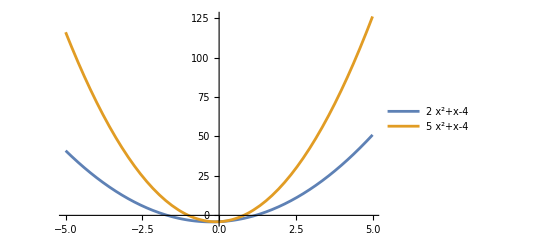

```mathematica
Plot[{2x^2+x-4,5x^2+x-4},{x,-5,5},PlotLegends->"Expressions"]
```

```mathematica
(*higher the a, more the fuckin' curvature*)
```

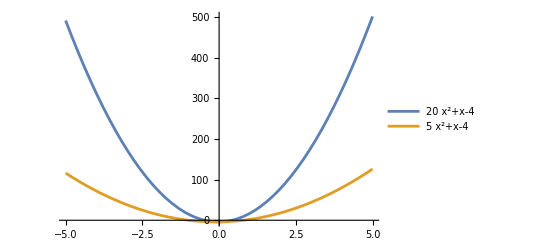

```mathematica
Plot[{20x^2+x-4,5x^2+x-4},{x,-5,5},PlotLegends->"Expressions"]
```

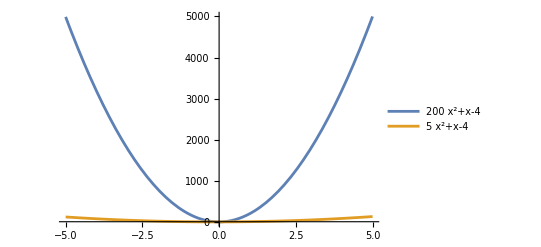

```mathematica
Plot[{200x^2+x-4,5x^2+x-4},{x,-5,5},PlotLegends->"Expressions"]
```

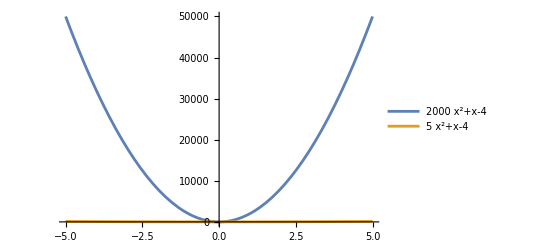

```mathematica
Plot[{2000x^2+x-4,5x^2+x-4},{x,-5,5},PlotLegends->"Expressions"]
```

```mathematica
(* by courtesy of Arnav K*)
```

```mathematica
Manipulate[Plot[a*x^2+b*x+c,{x,-5,5},PlotRange->{{-5,5},{-10,10}}],{{a,1},-5,5},{{b,0},-5,5},{{c,0},-5,5}]
```